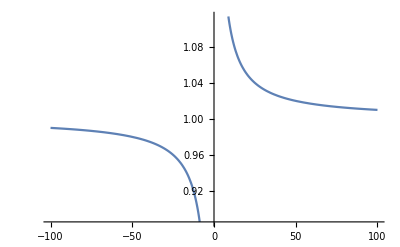

```mathematica
Plot[1+1/x,{x,-100,100}]
```

```mathematica
NDSolve[1/((r^2)[t])D[r[t]^2 *r'[t]],r[t],{t,-1,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of (r[t]^2 r'[t])/(r^2[t]) in the first argument (r[t]^2 r'[t])/(r^2[t]).

NDSolve[(r[t]^2 r'[t])/(r^2[t]),r[t],{t,-1,1}]

```mathematica
s=NDSolve[{y''[x]+Sin[y[x]] y[x]==0,y[-1]==1,y'[1]==0},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

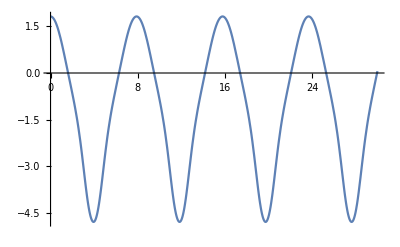

```mathematica
Plot[Evaluate[y[x] /. s], {x, 0, 30}, PlotRange -> All]
```

```mathematica
DSolve[1/((r^2)[t])D[{r[t]^2 *r'[t]},t]==0,r[t],{t,0,5}]
```

DSolve::dvnoarg: The function r appears with no arguments.

DSolve[{(2 r[t] r'[t]^2+r[t]^2 r''[t])/(r^2[t])}==0,r[t],{t,0,5}]

{{y→Function[{x},(ⅇ^(-x/2) C[1] (-[ⅇ^(ⅈ x)] [1]+[1] [ⅇ^(ⅈ x)]))/[1]]}}

```mathematica
D[r[t]^2*r'[t],t]
```

2 r[t] r'[t]^2+r[t]^2 r''[t]

```mathematica
DSolve[{(2 ψ[r] ψ'[r]^2+ψ[r]^2 ψ''[r])/ψ[r]^2==0},ψ[r],r]
```

{{ψ[r]→(3 r-C[1])^(1/3) C[2]}}

```mathematica
DSolve[{1/r^2 D[r^2*ψ'[r],r]==0, ψ[0]==0},ψ[r],r]
```

DSolve::deqn: Equation or list of equations expected instead of 0 in the first argument {(2 r ψ'[r]+r^2 ψ''[r])/r^2==0,0}.

DSolve[{(2 r ψ'[r]+r^2 ψ''[r])/r^2==0,0},ψ[r],r]

```mathematica
DSolve[{1/r^2 D[r^2*ψ'[r],r]==0,ψ[∞]==1},ψ[r],r]
```

{{ψ[r]→(r-C[1])/r}}

```mathematica
Simplify[{{ψ[r]->(r-C[1])/r}}]
```

{{ψ[r]→1-C[1]/r}}

```mathematica
DSolve[{1/r^2 D[r^2*ψ'[r],r]==0,ψ[∞]==1},ψ[r],r]
```

{{ψ[r]→(r-C[1])/r}}

```mathematica
Simplify[DSolve[{1/r^2 D[r^2*ψ'[r],r]==0,ψ[∞]==1},ψ[r],r]]
```

{{ψ[r]→1-C[1]/r}}

```mathematica
Simplify[DSolve[{1/r^2 D[r^2*ψ'[r],r]==0,ψ[∞]==1},ψ[r],r]]
```

{{ψ[r]→1-C[1]/r}}

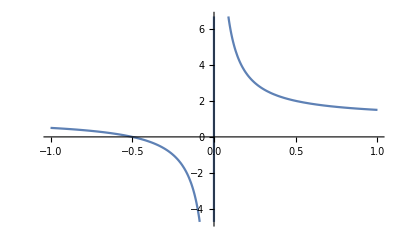

```mathematica
Plot[1+a/r/.a->0.5,{r,-1,1}]
```